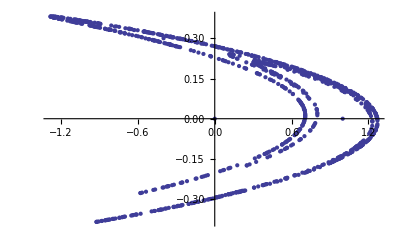

```mathematica
(* the Hénon map *)
f[{x_,y_}]={y+1-1.4 x^2,0.3 x};
hpic=ListPlot[NestList[f,{0,0},1000]]
```

```mathematica
F[xys:{{_,_}..}]:=f/@RotateRight[xys];
```

We look for a period n solution, ie we want 
{x_(i+n),y_(i+n)}={x_i,y_i}
ie we want F({{x_0,y_0},...{x_(n-1),y_(n-1)}})={f({x_(n-1),y_(n-1)}),...f({x_(n-2),y_(n-2)})}={{x_0,y_0},...{x_(n-1),y_(n-1)}}.

```mathematica
n=7;
vars=Table[{x[k],y[k]},{k,1,n}];
orbits=Select[Chop[NSolve[F[vars]==vars,Flatten[vars]]],FreeQ[#,_Complex]&];
firstOrbit=First[orbits]
```

{x[1]→-0.285392,y[1]→-0.326186,x[2]→0.559786,y[2]→-0.0856176,x[3]→0.475678,y[3]→0.167936,x[4]→0.851159,y[4]→0.142703,x[5]→0.128443,y[5]→0.255348,x[6]→1.23225,y[6]→0.038533,x[7]→-1.08729,y[7]→0.369675}

```mathematica
(* the Fibonacci trace map *)
t[{x_,y_,z_}]={2x y-z,x,y};
```

```mathematica
(* a periodic orbit of period 6 *)
hpic=ListPlot3D[NestList[t,{1,0,0},1000],InterpolationOrder->0]
```

-Graphics3D-

```mathematica
(* an aperiodic sequence; the divergene is slow, indicating that z=0.1 is close to an energy level of the Hamiltonian, for coupling ρ=0.5 *)
z=0.1;
ρ=0.5;
hpic=ListPlot3D[NestList[t,{1-z/2,1-ρ z/2,1},200],InterpolationOrder->0,PlotRange->All]
```

-Graphics3D-

```mathematica
(* another period 6 orbit (Luck and Petritis, 1986) *)
X=(3+√(25+4(1-ρ)^2 z^2))/8;
α=X+√(X^2-X);
β=X-√(X^2-X);
hpic=ListPlot3D[NestList[t,{-α,-β,α},1000],InterpolationOrder->0,PlotRange->All]
```

-Graphics3D-

```mathematica
T[xyzs:{{_,_,_}..}]:=t/@RotateRight[xyzs];
```

```mathematica
Clear[z];
n=7;
vars=Table[{x[k],y[k],z[k]},{k,1,n}];
orbits=Select[Chop[NSolve[T[vars]==vars,Flatten[vars]]],FreeQ[#,_Complex]&];
firstOrbit=First[orbits]
```

NSolve::infsolns: Infinite solution set has dimension at least 1. Returning intersection of solutions with -100578\ x[1]/179719 + 139279\ x[2]/179719 + 161175\ x[3]/179719 + 110048\ x[4]/179719 + 190342\ x[5]/179719 + « 18 » + 126598\ z[4]/179719 + 147750\ z[5]/179719 - 145871\ z[6]/179719 - 192556\ z[7]/179719 == 1.

{x[1]→1.88529,y[1]→-0.452705,z[1]→-2.16641,x[2]→0.459446,y[2]→1.88529,z[2]→-0.452705,x[3]→2.18509,y[3]→0.459446,z[3]→1.88529,x[4]→0.122567,y[4]→2.18509,z[4]→0.459446,x[5]→0.0761946,y[5]→0.122567,z[5]→2.18509,x[6]→-2.16641,y[6]→0.0761946,z[6]→0.122567,x[7]→-0.452705,y[7]→-2.16641,z[7]→0.0761946}

```mathematica
{x0,y0,z0}={1.8852934743358263,-0.45270485401524563,-2.166409382723186};
seventhIterate=Nest[t,{x0,y0,z0},7];
seventhIterate-{x0,y0,z0}//Chop
```

{0,0,0}

```mathematica
hpic=ListPlot3D[NestList[t,{x0,y0,z0},25],InterpolationOrder->0,PlotRange->All]
```

-Graphics3D-